```mathematica
BellY[5,2,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

10 x_2 x_3

```mathematica
ChromaticPolynomial[CycleGraph[4],x]//Factor
```

(-1+x) x (3-3 x+x^2)

```mathematica
ChromaticPolynomial[CycleGraph[4],x]//CompleteBaseCoeff
```

{0,0,1,2,1}

```mathematica
Table[ChromaticPolynomial[CycleGraph[k],x]//CompleteBaseCoeff,{k,3,10}]//TableForm
```

0 | 0 | 0 | 1 |  |  |  |  |  |  | 
0 | 0 | 1 | 2 | 1 |  |  |  |  |  | 
0 | 0 | 0 | 5 | 5 | 1 |  |  |  |  | 
0 | 0 | 1 | 10 | 20 | 9 | 1 |  |  |  | 
0 | 0 | 0 | 21 | 70 | 56 | 14 | 1 |  |  | 
0 | 0 | 1 | 42 | 231 | 294 | 126 | 20 | 1 |  | 
0 | 0 | 0 | 85 | 735 | 1407 | 924 | 246 | 27 | 1 | 
0 | 0 | 1 | 170 | 2290 | 6363 | 6027 | 2400 | 435 | 35 | 1

```mathematica
Table[ChromaticPolynomial[PathGraph[Range[k]],x]//CompleteBaseCoeff,{k,3,10}]//TableForm
```

0 | 0 | 1 | 1 |  |  |  |  |  |  | 
0 | 0 | 1 | 3 | 1 |  |  |  |  |  | 
0 | 0 | 1 | 7 | 6 | 1 |  |  |  |  | 
0 | 0 | 1 | 15 | 25 | 10 | 1 |  |  |  | 
0 | 0 | 1 | 31 | 90 | 65 | 15 | 1 |  |  | 
0 | 0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 |  | 
0 | 0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 | 
0 | 0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1

```mathematica
ChromaticPolynomial[PathGraph[Range[4]],x]//CompleteBaseCoeff
```

{0,0,1,3,1}

```mathematica
Table[Length[FindFullFormula[CycleGraph[k]]],{k,3,10}]//TableForm
```

1
4
11
41
162
715
3425
17722

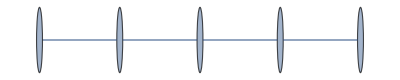
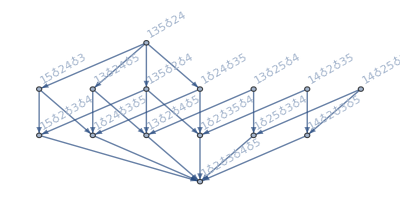
-Graphics-→-Graphics-5

```mathematica
With[{g=PathGraph[Range[5]]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]]
```


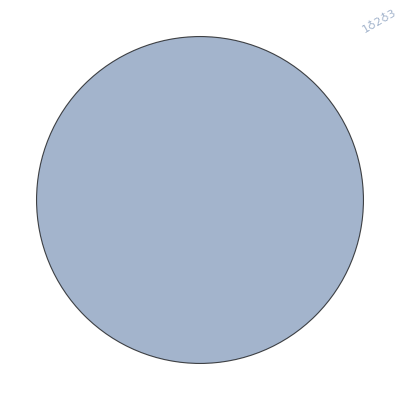
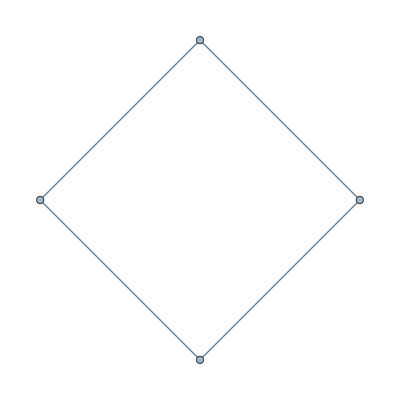
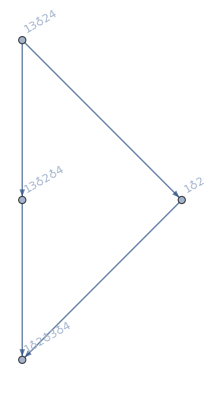
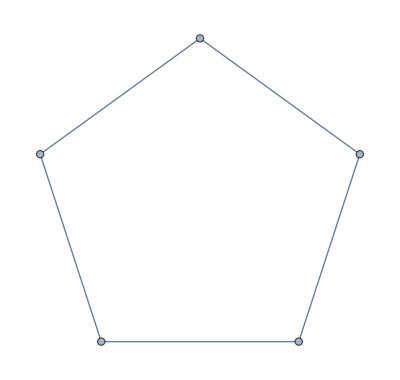
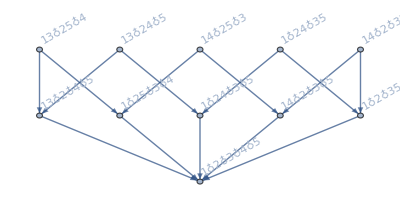
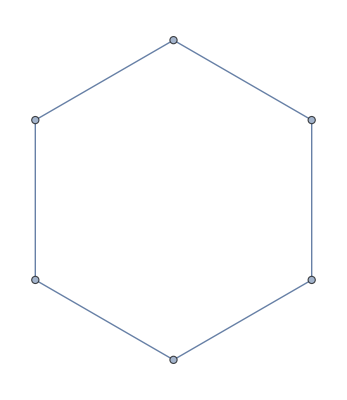
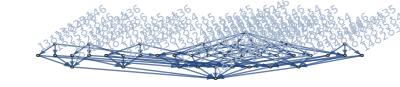
{-Graphics-→-Graphics-3,-Graphics-→-Graphics-4,-Graphics-→-Graphics-5,-Graphics-→-Graphics-6}

```mathematica
Table[With[{g=CycleGraph[k]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]],{k,3,6}]
```

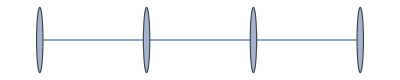
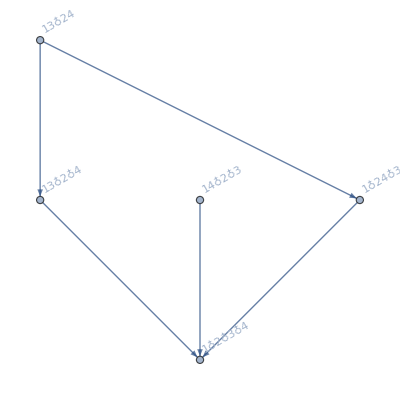
-Graphics-→-Graphics-4

```mathematica
With[{g=PathGraph[Range[4]]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]]
```

```mathematica
With[{g=CycleGraph[4]},g->Labeled[Graph[FormulaGraphReverse[FindFullFormula[g]]],Style[VertexCount[g],Red]]]
```

-Graphics-→-Graphics-4